```mathematica
ClearAll[Fdiv];
SetAttributes[Fdiv,HoldAll];
Off[NIntegrate::izero];
Off[General::stop];
```

```mathematica
WorkingPrec = 15;
MaxRec = 50;
```

```mathematica
Fdiv[Adensity_,Bdensity_,f_]:= Module[{adivbyb,functiontointegrate},
adivbyb[x_]:= Adensity[x] / Bdensity[x];
functiontointegrate[x_] := Expand[Bdensity[x]*Composition[f,adivbyb][x]];
Return  [NIntegrate[functiontointegrate[x], {x, 0.12,0.32},WorkingPrecision->WorkingPrec, MaxRecursion->MaxRec]];
]

(* NIntegrate[Expand[Bdensity[x]*Composition[f,Adensity[x]/Bdensity[x]][x]], {x,-2, 2}]; *)
```

```mathematica
(* All distances except Wasserstein *)
means = Subdivide[0.15,0.32, 20];
std = 0.005;

Adist := MixtureDistribution[{1.0,0.1},{NormalDistribution[means[[1]],std],NormalDistribution[means[[13]],0.0025]}];
Bdist := MixtureDistribution[{0.5,0.5},{NormalDistribution[means[[3]],std],NormalDistribution[means[[15]],std]}];
Cdist := MixtureDistribution[{1.0,0.1},{NormalDistribution[means[[5]],std],NormalDistribution[means[[17]],0.0025]}];
Ddist :=MixtureDistribution[{1.0,0.1},{NormalDistribution[means[[17]],std],NormalDistribution[means[[5]],0.0025]}];

Adensity[x_] := PDF[Adist,x];
Bdensity[x_] := PDF[Bdist,x];
Cdensity[x_] := PDF[Cdist,x];
Ddensity[x_] := PDF[Ddist,x];

Acum[x_] :=  CDF[Adist,x];
Bcum[x_] :=  CDF[Bdist,x];
Ccum[x_] :=  CDF[Cdist,x];
Dcum[x_] :=  CDF[Ddist,x];
```

```mathematica
(* Wasserstein distance *)
means = Subdivide[0.15,0.32, 10];
std = 0.005;
nearnessAD1 = 0.85;
nearnessAD2 =0.25;

Adist := MixtureDistribution[{1.2,1.0},{NormalDistribution[(1-nearnessAD1)*means[[1]] + nearnessAD1*(means[[3]]),std],NormalDistribution[(1-nearnessAD2)*means[[4]] + nearnessAD2*(means[[6]]),std]}];
Bdist := MixtureDistribution[{1.0,1.0},{NormalDistribution[means[[3]],std],NormalDistribution[means[[6]],std]}];
Cdist := MixtureDistribution[{1.0,1.0},{NormalDistribution[means[[4]],std],NormalDistribution[means[[5]],std]}];
Ddist :=MixtureDistribution[{1.0,1.2},{NormalDistribution[(1-nearnessAD2)*means[[5]] + nearnessAD2*(means[[3]]),std],NormalDistribution[(1-nearnessAD1)*means[[8]] + nearnessAD1*(means[[6]]),std]}];


Adensity[x_] := PDF[Adist,x];
Bdensity[x_] := PDF[Bdist,x];
Cdensity[x_] := PDF[Cdist,x];
Ddensity[x_] := PDF[Ddist,x];

Acum[x_] :=  CDF[Adist,x];
Bcum[x_] :=  CDF[Bdist,x];
Ccum[x_] :=  CDF[Cdist,x];
Dcum[x_] :=  CDF[Ddist,x];
```

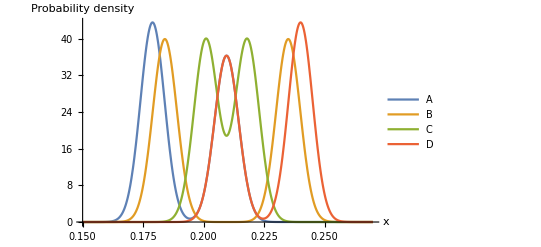

densityplot.pdf

```mathematica
plot = Plot[{Adensity[x],Bdensity[x],Cdensity[x],Ddensity[x]},{x, 0.15,0.27},  PlotLegends->{"A","B","C", "D"}, PlotRange->Full, AxesLabel->{"x","Probability density"}]
Export["densityplot.pdf",plot]
```

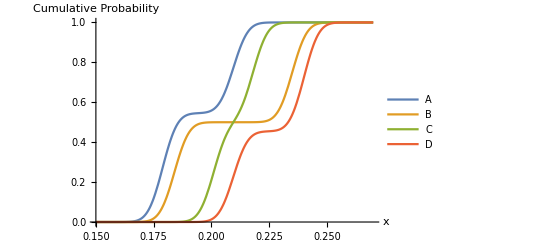

cumulativedensityplot.pdf

```mathematica
plot = Plot[{Acum[x],Bcum[x],Ccum[x],Dcum[x]},{x, 0.15,0.27}, PlotLegends->{"A","B","C", "D"}, PlotRange->Full, AxesLabel->{"x","Cumulative Probability"}]
Export["cumulativedensityplot.pdf",plot]
```

```mathematica
fKL[x_]:= x * Log[x]
fJS[x_] := x * Log[2*x / (x +1)]+ Log[2/(x+1)]
fTV[x_]:= 0.5*Abs[x -1]
fHellsquared[x_]:= (1 - Sqrt[x])^2
```

```mathematica
Fdiv[Adensity,Bdensity,fKL]
Fdiv[Adensity,Bdensity,fJS]
```

4.32382651855961

0.757394900014829

```mathematica
ffunctions = {fKL,fJS,fTV,fHellsquared};
distributions={Adensity,Bdensity,Cdensity,Ddensity};
cumdistributions={Acum,Bcum,Ccum,Dcum};
listOfMatrices=ConstantArray[0,{7,4,4}];
WriteString["stdout","dist1,dist2,KL, JS, Total Variation, Helligner, Wasserstein, Wasserstein without abs, Total variation altern."]
For[j=0,j<4,j++,
For[k=0,k<4,k++,
distcurrent1 = distributions[[j+1]];
distcurrent2 = distributions[[k+1]];
cumdistcurrent1 = cumdistributions[[j+1]];
cumdistcurrent2 = cumdistributions[[k+1]];
WriteString["stdout","\n",distcurrent1, ",", distcurrent2, ","];
For[i=0,i<3,i++,
fcurrent = ffunctions[[i+1]];
res = Round[Fdiv[distcurrent1,distcurrent2,fcurrent],0.001];
listOfMatrices[[i+1,j+1,k+1]] =res;
WriteString["stdout", ToString[res], "," ];
];
res = Round[NIntegrate[0.5*Abs[distcurrent1[x] - distcurrent2[x]],{x,0.1,0.35}, WorkingPrecision->WorkingPrec, MaxRecursion->MaxRec],0.001];
Print["TV alt:",res];
listOfMatrices[[7,j+1,k+1]] = res;
fcurrent = ffunctions[[4]];
res = Round[Sqrt[Fdiv[distcurrent1,distcurrent2,fcurrent]], 0.001];
listOfMatrices[[4,j+1,k+1]] =res;
WriteString["stdout", ToString[res], "," ];
(*Wasserstein*)
res = Round[NIntegrate[Abs[cumdistcurrent1[x] - cumdistcurrent2[x]],{x, 0.1,0.35}, WorkingPrecision->WorkingPrec, MaxRecursion->MaxRec], 0.001];
listOfMatrices[[5,j+1,k+1]] =res;
WriteString["stdout", ToString[res]];
(*Wasserstein without abs*)
res = Round[NIntegrate[cumdistcurrent1[x] - cumdistcurrent2[x],{x, 0.1,0.35}, WorkingPrecision->WorkingPrec, MaxRecursion->MaxRec], 0.001];
listOfMatrices[[6,j+1,k+1]] =res;
WriteString["stdout", ToString[res]];
];
];
```

dist1,dist2,KL, JS, Total Variation, Helligner, Wasserstein, Wasserstein without abs, Total variation altern.
Adensity,Adensity,0.,0.,0.,0.,0.0.
Adensity,Bdensity,4.324,0.757,0.672,1.011,0.0170.017
Adensity,Cdensity,5.295,0.635,0.616,0.898,0.0170.017
Adensity,Ddensity,10.316,0.754,0.545,1.04,0.0330.033
Bdensity,Adensity,6.738,0.757,0.672,1.011,0.017-0.017
Bdensity,Bdensity,0.,0.,0.,0.,0.0.
Bdensity,Cdensity,5.78,1.158,0.911,1.236,0.0170.
Bdensity,Ddensity,6.738,0.757,0.672,1.011,0.0170.017
Cdensity,Adensity,1.501,0.635,0.616,0.898,0.017-0.017
Cdensity,Bdensity,5.692,1.158,0.911,1.236,0.0170.
Cdensity,Cdensity,0.,0.,0.,0.,0.0.
Cdensity,Ddensity,1.501,0.635,0.616,0.898,0.0170.017
Ddensity,Adensity,10.316,0.754,0.545,1.04,0.033-0.033
Ddensity,Bdensity,4.324,0.757,0.672,1.011,0.017-0.017
Ddensity,Cdensity,5.295,0.635,0.616,0.898,0.017-0.017
Ddensity,Ddensity,0.,0.,0.,0.,0.0.

TV alt:0.

TV alt:0.672

TV alt:0.616

TV alt:0.545

TV alt:0.672

TV alt:0.

TV alt:0.911

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1.25063339646601×10^-17 and 3.43352006816621×10^-18 for the integral and error estimates.

TV alt:0.672

TV alt:0.616

TV alt:0.911

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -1.25063339646601×10^-17 and 3.43352006816621×10^-18 for the integral and error estimates.

TV alt:0.

TV alt:0.616

TV alt:0.545

TV alt:0.672

TV alt:0.616

TV alt:0.

```mathematica
For[i=1,i≤ 7,i++,
Print [{"KL", "JS", "Total Variation", "Helligner", "Wasserstein","Wasserstein without abs","Total variation-alternative computation"}[[i]]];
Print[listOfMatrices[[i]] // MatrixForm]
]
```

KL

(0. | 4.324 | 5.295 | 10.316
6.738 | 0. | 5.78 | 6.738
1.501 | 5.692 | 0. | 1.501
10.316 | 4.324 | 5.295 | 0.)

JS

(0. | 0.757 | 0.635 | 0.754
0.757 | 0. | 1.158 | 0.757
0.635 | 1.158 | 0. | 0.635
0.754 | 0.757 | 0.635 | 0.)

Total Variation

(0. | 0.672 | 0.616 | 0.545
0.672 | 0. | 0.911 | 0.672
0.616 | 0.911 | 0. | 0.616
0.545 | 0.672 | 0.616 | 0.)

Helligner

(0. | 1.011 | 0.898 | 1.04
1.011 | 0. | 1.236 | 1.011
0.898 | 1.236 | 0. | 0.898
1.04 | 1.011 | 0.898 | 0.)

Wasserstein

(0. | 0.017 | 0.017 | 0.033
0.017 | 0. | 0.017 | 0.017
0.017 | 0.017 | 0. | 0.017
0.033 | 0.017 | 0.017 | 0.)

Wasserstein without abs

(0. | 0.017 | 0.017 | 0.033
-0.017 | 0. | 0. | 0.017
-0.017 | 0. | 0. | 0.017
-0.033 | -0.017 | -0.017 | 0.)

Total variation-alternative computation

(0. | 0.672 | 0.616 | 0.545
0.672 | 0. | 0.911 | 0.672
0.616 | 0.911 | 0. | 0.616
0.545 | 0.672 | 0.616 | 0.)